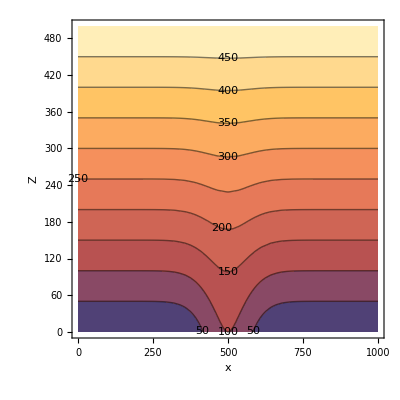

```mathematica
(* Define parameters *)
x0=0; x1=1000;
y0=0; y1=1000;
hh=100; hw=100;
hx=(x0+x1)/2; hy=(y0+y1)/2;

(* Define the hill *)
hill[x_,y_]=hh Exp[-((x-hx)^2+(y-hy)^2)/hw^2];
(* Define the vertical coordinates *)
s1=150; s2=150; H=500;
b1[Z_]=Sinh[(H-Z)/s1]/Sinh[H/s1];b2[Z_]=Sinh[(H-Z)/s2]/Sinh[H/s2];
h1[x_,y_]=hill[x,y];
(*h2[x_,y_]=0x y;*)
z[x_,y_,Z_]=Z+h1[x,y]b1[Z]; (*+h2[x,y]b2[Z];*)

(* Plot the hill
Plot3D[hill[x,y],{x,x0,x1},{y,y0,y1},PlotRange->All]
 *)

(*Generate 10 uniformly spaced Z values*)
zValues=Range[0,H,H/10];

(*Plot vertical contours at y=hy*)
ContourPlot[
z[x,hy,Z],
{x,x0,x1},{Z,0,H},
Contours->zValues,
FrameLabel->{"x","Z"},
ContourLabels->True
]
```